```mathematica
(*************************  NIPOTI  ************************)

Manipulate[
coloreDenominatore = Blue;
coloreNumeratore = Red;
spaceX = 6.5;
objNipoti = {};    (* oggetto che contiene la lista degli oggetti grafici che compongono il singolo nipote (line, line, circle etc.)*)
plotRange = 15;
offsetX = -19;
offsetY = 3;
For[i = 0, i< numeroNipoti,i++,
AppendTo[objNipoti,
{Thickness[.01],
Line[{{0 + (i*spaceX)+offsetX,0},{2 + (i*spaceX)+offsetX,3}}],(*Gamba destra*)
Line[{{2 + (i*spaceX)+offsetX,3},{4 + (i*spaceX)+offsetX,0}}],(*Gamba sinistra*)
Line[{{2 + (i*spaceX)+offsetX,3},{2 + (i*spaceX)+offsetX,7}}], (*Busto*)
Line[{{2 + (i*spaceX)+offsetX,7},{4 + (i*spaceX)+offsetX,5}}], (* Braccio destro*)
Line[{{2 + (i*spaceX)+offsetX,7},{0 + (i*spaceX)+offsetX,5}}], (* Braccio sinistro*)

Circle[{2 + (i*spaceX)+offsetX,8.5},1.4]

}]
(*{Black,Rectangle[{(i*spaceX)+offsetX,0},{3+(i*spaceX)+ offsetX,6}], Disk[{1.5+ (i*spaceX)+offsetX, 6}, 1.5], Black, Rectangle[{1+(i*spaceX)+offsetX,7},{2+ (i*spaceX)+offsetX,9}]}}*)
];
objBicchieri = {};
offsetX = -9;
offsetY = -6;
(* For[i = 0, i< numeroBicchieri,i++,
AppendTo[objBicchieri,{Black,Circle[{(i*2)+offsetX,0 + offsetY},1]}]
]; *)
Graphics[{
objNipoti,
objBicchieri
},PlotRange->{{-20,40},{-15,15}}]
(*paramentri primo slider*)
,{
{numeroNipoti,1,(*valore iniziale slider numeratore*)
		Style["Numero Nipoti",Directive[coloreNumeratore,Large]]},
	1,8,1,(*valore iniziale, valore finale, step di incremento/decremento slider*)
	Appearance->{"Labeled"},
	AppearanceElements->{"InputField"},
	LabelStyle->Directive[coloreNumeratore,Large],
	ImageSize->170
	}(*,(*--fine slider numeratore*)
{
{numeroBicchieri,2,Style["Numero bicchieri",Directive[coloreDenominatore,Large]]}
,1,10,1,
	Appearance->{"Labeled"},
	AppearanceElements->{"InputField"},(*rimuovo tutto tranne l'inputField*)
	LabelStyle->Directive[coloreDenominatore,Large],ImageSize->170}*)
]
```

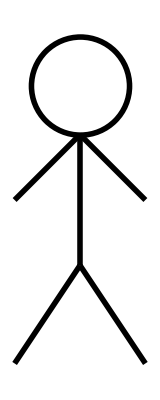

```mathematica
Graphics[{Thickness[.01],
Line[{{0,0},{2,3}}],(*Gamba destra*)
Line[{{2,3},{4,0}}],(*Gamba sinistra*)
Line[{{2,3},{2,7}}], (*Busto*)
Line[{{2,7},{0,5}}],
Line[{{2,7},{4,5}}],
Circle[{2,8.5},1.5]

}, PlotRange-> Automatic]
```

```mathematica
(* FUNZIONE che riempre l'array objMonete. Ad ogni iterazione vengono create 3 monete.
   In base al parametro passato vengono disegnate 3*x monete.*)
getMoneteArray[y_] := (

objMonete = {};
spaceXMonete = 70;
offsetX = -700;
raggio1 = 22;
raggio2 = 32;
sizeDollaro = 20;
offsetY2 = 350;
quota1 = 0; (* Le monete vengono visualizzare in colonne da 3 partendo da sinistra. Quindi ci sono 3 diverse quote.*)
quota2 = -70;
quota3 = -140;

For[i=0, i<y, i++,
AppendTo[objMonete,
{(*moneta 1*)
Thick,Yellow,EdgeForm[{Thick, Black}], Disk[{0 +(i*spaceXMonete) + offsetX,quota1 +offsetY2}, raggio2],Thick,Yellow,EdgeForm[{Thick, Black}], Disk[{0 +(i*spaceXMonete) + offsetX,quota1+offsetY2},raggio1],Text[Style["€",Large,Bold, Black, Thick, FontSize->sizeDollaro], {0 + (i*spaceXMonete) + offsetX,quota1 + offsetY2 },Automatic ],
(*moneta 2*)
Thick,Yellow,EdgeForm[{Thick, Black}], Disk[{0 +(i*spaceXMonete) + offsetX,quota2 +offsetY2}, raggio2],Thick,Yellow,EdgeForm[{Thick, Black}], Disk[{0 +(i*spaceXMonete) + offsetX,quota2 +offsetY2},raggio1],Text[Style["€",Large,Bold, Black, Thick, FontSize->sizeDollaro], {0 + (i*spaceXMonete) + offsetX, quota2  + offsetY2 },Automatic ],
(*moneta 3*)
Thick,Yellow,EdgeForm[{Thick, Black}], Disk[{0 +(i*spaceXMonete) + offsetX,quota3+offsetY2}, raggio2],Thick,Yellow,EdgeForm[{Thick, Black}], Disk[{0 +(i*spaceXMonete) + offsetX,quota3+offsetY2},raggio1],Text[Style["€",Large,Bold, Black, Thick, FontSize-> sizeDollaro], {0 + (i*spaceXMonete) + offsetX,quota3 + offsetY2 },Automatic ]}
]];

objMonete
)

(* FUNZIONE che riempe l'array objNipoti (3 figure) *)
getNipotiArray[x_] := (
objNipoti = {};
spaceX = 510;
spaceY = -200;
offsetX = -600;

For[i=0, i<x, i++,
AppendTo[objNipoti,
{Thickness[.005],
Line[{{0 + (i*spaceX)+offsetX,0 + spaceY},{40 + (i*spaceX)+offsetX,60+ spaceY}}],           (*Gamba destra*)
Line[{{40 + (i*spaceX)+offsetX,60+ spaceY},{80+ (i*spaceX)+offsetX,0 + spaceY}}],          (*Gamba sinistra*)
Line[{{40 + (i*spaceX)+offsetX,60 + spaceY},{40 + (i*spaceX)+offsetX,140 + spaceY}}],   (*Busto*)
Line[{{40 + (i*spaceX)+offsetX,140 + spaceY},{80 + (i*spaceX)+offsetX,100 + spaceY}}], (* Braccio destro*)
Line[{{40 + (i*spaceX)+offsetX,140 + spaceY},{0 + (i*spaceX)+offsetX,100 + spaceY}}],   (* Braccio sinistro*)

Circle[{38 + (i*spaceX)+offsetX,161 + spaceY},20.4]                                                                                     (*Testa*)

}
]];
objNipoti
)

(* Funzione per calcolare l'array di monete che spettano ad ogni nipote, in base a quante monete puo dare il nonno*)
getDivisioneMonete[x_, offsetX_] := (
objFinal = {};
spaceXMonete = 35;
raggio1 = 11;
raggio2 = 16;
sizeDollaro = 10;
offsetY2 = -300;

(* divisione effettiva per calcolare le monete per ogni nipote  *)
y = x/3;

For[i=0, i<y, i++,
AppendTo[objFinal, {Thick,Yellow,EdgeForm[{Thick, Black}], Disk[{0 +(i*spaceXMonete) + offsetX,0+offsetY2}, raggio2],Thick,Yellow,EdgeForm[{Thick, Black}], Disk[{0 +(i*spaceXMonete) + offsetX,0+offsetY2},raggio1],Text[Style["€",Large,Bold, Black, Thick, FontSize-> sizeDollaro], {0 + (i*spaceXMonete) + offsetX,0+ offsetY2},Automatic ]}]
];
objFinal
)

getEsempioNipoti[] := (
(* MONETE NIPOTI *)
coloreNumeratore = Red;
valoreNumeroMonete = 0;

Manipulate[

If[ valoreNumeroMonete ≠ numeroMonete,
valoreNumeroMonete = numeroMonete;

objMonete = getMoneteArray[numeroMonete/3];
objFinal1 = getDivisioneMonete[numeroMonete, -700];
objFinal2 = getDivisioneMonete[numeroMonete, -200];
objFinal3 = getDivisioneMonete[numeroMonete, 300];
objNipoti = getNipotiArray[3];
paghetta = numeroMonete/3;
]; (*Chiusura IF*)
Graphics[{
Text[Style["Monete del nonno",FontSize->40, Bold, Black],{-400,450}], (*Label "Monete del nonno"*)
objNipoti,                                                                                                                                   (* Array contenente gli oggetti grafici per disegnare i nipoti*)
Text[Style["Nipoti",FontSize->40, Bold, Black],{-590,70}],
objMonete,                                                                                                                                   (* Array contenente oggetti grafici per disegnare le monete del nonno *)
objFinal1,                                                                                                                                   (* Array contenente oggetti graficiper disegnare le monete del nonno *)
objFinal2,
objFinal3,
Text[Style[paghetta,FontSize->20, Bold, Black],{-550,-380}],           (* Text contenenti il numero relativo alle monete che spettano ad ogni Nipote *)
Text[Style[paghetta,FontSize->20, Bold, Black],{  -50,-380}],           
Text[Style[paghetta,FontSize->20, Bold, Black],{ 450,-380}],
Text[Style["Euro",FontSize->20, Bold, Black],{-550,-430}],                (*Text contenenti la stringa "Euro" mostrate sotto le monete di ogni Nipote*)
Text[Style["Euro",FontSize->20, Bold, Black],{  -50,-430}],
Text[Style["Euro",FontSize->20, Bold, Black],{ 450,-430}],
{Black,Thick,Line[{{-290,-460},{-290,0}}]},                                                (*Linea divisoria sinistra *)
{Black,Thick,Line[{{210,-460},{210,0}}]}                                                         (* Linea divisoria destra *)
},ImageSize->{800, 500}, PlotRange->{{-800,800},{-500,500}}]

(*paramentri primo slider*)
,{{numeroMonete,3,                                                                                                                   (*valore iniziale slider numeratore*)
		Style["Numero Monete",Directive[coloreNumeratore,Large]]},
	3,30,3,                                                                                                                                          (*valore iniziale, valore finale, step di incremento/decremento slider*)
	Appearance->{"Labeled"},
	AppearanceElements->{"InputField"},
	LabelStyle->Directive[coloreNumeratore,Large],
	ImageSize->170
	}

]

)
```

```mathematica
getEsempioNipoti[]
```